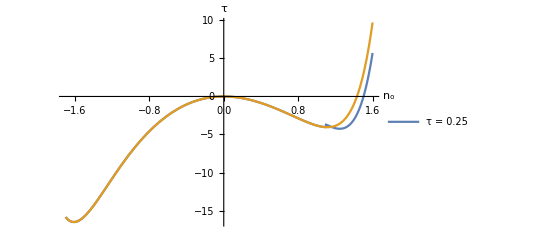

.png

```mathematica
FvdW = τ*(no + 1)* Log[((no + 1)*(1 - b))/(1 - (no + 1)*b)]- a1*no^2 - τ/(1 - b) * no;
FvdWexpansion =Normal[Series[FvdW,{no, 0.0, 10}]];
Fex =-Bx*τ*Exp[-τ/Tm]*3*(ϕ)^2 + d/2* no^2 ; (*???*)
Fzeta1 = a2/2 (6 ϕ^2);
Fzeta2 = a3/3 (18*no*ϕ^2+12*ϕ^3);
Fzeta3 = a4/4(36*no^2*ϕ^2+48*no*ϕ^3+90*ϕ^4);
F = FvdWexpansion+Fex +  Fzeta1 + Fzeta2 + Fzeta3;

nmin = -2.5;(*-1.5;*)
nmax = 2.0;(*2.0;*) 
(*Fsubs = F/.{ a1-> 8.5, b-> 0.5,a2 -> 3.0+4.* τ+0.1* τ^2, a3-> -1.2-0.6* τ+0.1
* τ^2,a4->0.08, Bx -> 1.5, Tm -> 1.0, d ->3.3*τ}; a2 -> 2.9+4.2* τ+0.05* τ^2, a3-> -1.15-0.7* τ+0.3* τ^2,a4->0.065,*)
Fsubs = F/.{ a1-> 6.9*(1 - 0.2*no), b-> 0.5,a2 -> 2.8+4.0* τ+0.1* τ^2, a3-> -1.2-0.48* τ+0.1* τ^2,a4->0.08, Bx -> 1.5, Tm -> 1.0, d ->3.3*τ};
Ffcc[n0_, T_]:=FindMinimum[{Fsubs/.{ no->n0,τ -> T}, {ϕ} ∈ Reals, ϕ≥ 0
}, {ϕ, 1.0}][[1]];
Fl[n0_, T_] := Fsubs/.{ϕ -> 0, no->n0, τ -> T}; 
plottingT = 0.2;
p1 = Show[Plot[{ Ffcc[nn,0.25], Fl[nn,0.25]}, {nn, -1.7, 1.6}, PlotLegends->{Style["τ = 0.25" ,Black,Bold,14]},AxesLabel->{Style["n_o",Black, FontSize->18], Style["τ",Black, FontSize-> 18]}, TicksStyle->Directive[Black, 12]]]
Export[".png",p1]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

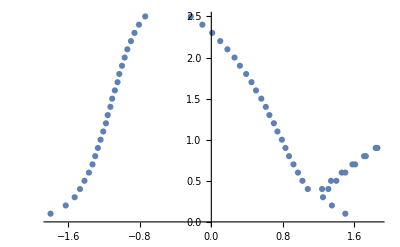

```mathematica
commonTangent = {};
spinodal = {};
convexStep = 0.01;
For[T= 0.1, T< 2.6, T = T + 0.1, 
	fcn=Table[{i,Ffcc[i, T]},{i,nmin,nmax,convexStep}]  ;
	b = Interpolation[fcn, Method-> "Spline"];
	spin = b'';
	s1=x/.FindRoot[spin[x]==0,{x,-0.7}];
	s2=x/.FindRoot[spin[x]==0,{x,0.2}];
	s3=x/.FindRoot[spin[x]==0,{x,0.7}];
	convHull = ConvexHullMesh[fcn];
	convHulln = MeshCoordinates[convHull][[All, 1]];

	len = Length[convHulln];
	dummy = {};

	For[i =  len, i>2, i--,
	If[Abs[convHulln[[i]] -(convHulln[[i - 1]] )]- convexStep>0.000001  ,
	dummy = Append[dummy, {convHulln[[i]], convHulln[[i - 1]]}]
	]
	];
	
	For[ j = 1, j <= Length[dummy], j++,
	commonTangent = Append[commonTangent, {dummy[[j,1]], T}];
	commonTangent = Append[commonTangent, {dummy[[j,2]], T}];
	];
If[T<2.0,
If[Abs[s1] > 0.0001, 
spinodal=Append[spinodal,{s1,T}];
];
If[Abs[s2] > 0.0001,
spinodal=Append[spinodal,{s2,T}];
];
If[Abs[s3] > 0.0001,
spinodal=Append[spinodal,{s3,T}];
];
];

];
ListPlot[commonTangent]
```

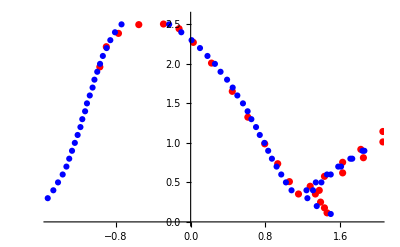

```mathematica
AluminumData = {{0.030581039755351702,5.161381459705115},
{0.10703363914373087,5.833879397552119},
{0.25,6.278737700530888},
{0.4892966360856268,6.57},
{0.7798165137614679,6.59},
{0.9633027522935778,6.434438263328991},
{1.1314984709480123,5.978548334019763},
{1.3455657492354738,5.289373746757306},
{1.5902140672782874,4.348083467104509},
{1.7737003058103973,3.4878129953107435},
{1.972477064220183,2.599522716843655},
{2.1253822629969417,1.9374657885819826},
{2.262996941896024,1.3417128354799117},
{2.3700305810397553,0.929148449227118},
{2.5076452599388377,1.187047465568134},
{2.6758409785932717,1.5165302021262907},
{2.8899082568807337,1.9855111964445817},
{3.1039755351681957,2.4153425010859464},
{3.3639143730886847,3.011087696068115},
{3.6238532110091746,3.5743040182210497},
{3.883792048929663,4.1401995764592225},
{4.128440366972477,4.679643463562064},
{4.37308868501529,5.161381459705115},
{4.602446483180428,5.692711160586989},
{4.81651376146789,6.126804780573316},
{5,6.434438263328991},
{4.984709480122323,6.126804780573316},
{4.755351681957185,5.692711160586989},
{4.403669724770641,4.914613414182185},
{4.143730886850152,4.348083467104509},
{3.8685015290519877,3.753773681925604},
{3.3639143730886847,2.663985857258772},
{3.1345565749235473,2.136914933341561},
{2.8899082568807337,1.6321721285632744},
{2.6146788990825685,1.0502110796366664},
{2.568807339449541,0.929148449227118},
{2.6299694189602443,0.6593999899229991},
{2.6758409785932717,0.4679643463562064},
{2.706422018348624,0.30110876960681165}};

rhoBar = 1.1;
T0 =0.38;(*1/K*)
Do[	
	AluminumData[[i,1]] = (AluminumData[[i,1]] - rhoBar )/rhoBar;
	AluminumData[[i,2]] = AluminumData[[i,2]]*T0 ;(*fit the temperature data*),
{i, 1, Length[AluminumData]}
]
p1 = ListPlot[AluminumData, PlotStyle->Red, PlotRange->{{-1.5, 2}, {0, 2.6
}}];
p2 = ListPlot[spinodal, AxesLabel -> {"no", "τ"}];
p3 = ListPlot[commonTangent, AxesLabel -> {"no", "τ"}, PlotStyle-> Blue];
Show[ p1,p3]
```

```mathematica
2
```

2

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

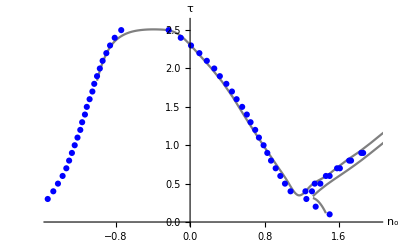

```mathematica
AluminumData1 = {{0.030581039755351702,5.161381459705115},
{0.10703363914373087,5.75},
{0.25,6.3},
{0.4892966360856268,6.57},
{0.7798165137614679,6.5939998992299875},
{0.9633027522935778,6.434438263328991},
{1.1314984709480123,5.978548334019763},
{1.3455657492354738,5.289373746757306},
{1.5902140672782874,4.348083467104509},
{1.7737003058103973,3.4878129953107435},
{1.972477064220183,2.599522716843655},
{2.1253822629969417,1.9374657885819826},
{2.262996941896024,1.3417128354799117},
{2.3700305810397553,0.929148449227118},
{2.5076452599388377,1.187047465568134},
{2.6758409785932717,1.5165302021262907},
{2.8899082568807337,1.9855111964445817},
{3.1039755351681957,2.4153425010859464},
{3.3639143730886847,3.011087696068115},
{3.6238532110091746,3.5743040182210497},
{3.883792048929663,4.1401995764592225},
{4.128440366972477,4.679643463562064},
{4.37308868501529,5.161381459705115},
{4.602446483180428,5.692711160586989},
{4.81651376146789,6.126804780573316},
{5,6.434438263328991}};
AluminumData2 ={{4.984709480122323,6.126804780573316},
{4.755351681957185,5.692711160586989},
{4.403669724770641,4.914613414182185},
{4.143730886850152,4.348083467104509},
{3.8685015290519877,3.753773681925604},
{3.3639143730886847,2.663985857258772},
{3.1345565749235473,2.136914933341561},
{2.8899082568807337,1.6321721285632744},
{2.6146788990825685,1.0502110796366664},
{2.568807339449541,0.929148449227118}}; 
AluminumData3 = {{2.6299694189602443,0.6593999899229991},
{2.6758409785932717,0.4679643463562064},
{2.706422018348624,0.30110876960681165}};
rhoBar = 1.1;
T0 =0.38;(*1/K*)
Do[	
	AluminumData1[[i,1]] = (AluminumData1[[i,1]] - rhoBar )/rhoBar;
	AluminumData1[[i,2]] = AluminumData1[[i,2]]*T0 ;(*fit the temperature data*),
{i, 1, Length[AluminumData1]}
]

Do[	
	AluminumData2[[i,1]] = (AluminumData2[[i,1]] - rhoBar )/rhoBar;
	AluminumData2[[i,2]] = AluminumData2[[i,2]]*T0 ;(*fit the temperature data*),
{i, 1, Length[AluminumData2]}
]
Do[	
	AluminumData3[[i,1]] = (AluminumData3[[i,1]] - rhoBar )/rhoBar;
	AluminumData3[[i,2]] = AluminumData3[[i,2]]*T0 ;(*fit the temperature data*),
{i, 1, Length[AluminumData3]}
]


g1 = ListPlot[AluminumData1];
g2 = ListPlot[AluminumData2];
g3 = ListPlot[AluminumData3];

A= Interpolation[AluminumData1, Method-> "Spline"];
B = Interpolation[AluminumData2, Method-> "Spline"];
H = Interpolation[AluminumData3, Method -> "Spline"];

g4 = Plot[A[x], {x, -1., 5}, PlotStyle->Gray, PlotRange->{{-1.5, 2.}, {0, 2.6
}}, AxesLabel->{Style["n_o",Black, FontSize->15], Style["τ",Black, FontSize-> 20]}, TicksStyle->Directive[Black, 10]];
g5 = Plot[B[x], {x,1.32, 5.}, PlotStyle->Gray];
g6 = Plot[H[x], {x, 1.32, 1.46}, PlotStyle-> Gray];
Show[g4, g5, g6, p3]
```